```mathematica
f[x_]:=a x^2 + b x^4 +c x+d x^3+e x^5+f x^6
```

```mathematica
s=Solve[{f'[0]==0,f''[0]==0, f'[L]==0,f''[L]==0,f[0]==f[L]},{a,b,c,d,e}]
```

{{a→0,b→3 f L^2,c→0,d→-f L^3,e→-3 f L}}

```mathematica
f[x]/.s[[1]]/.{f->1}//FullSimplify
```

-(L-x)^3 x^3

```mathematica
L=1
```

1

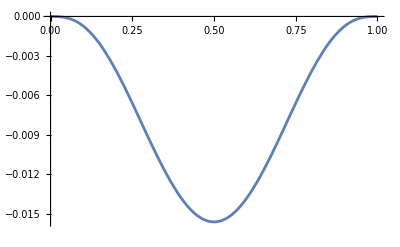

```mathematica
Plot[f[x]/.s[[1]]/.{f->1},{x,0,L}]
```